## Import Qgraph output

```mathematica
SMHFeynmanRules=Import["./amp_generation/SMHFeynmanRulesTop.m"];(* this file contains feynrules *)
Get["./amp_generation/generate_amplitudes.m"];(* this file generates amplitude *)
(* load qgraf*)
ggHH=QImport["./amp_generation/ggHH.qgr"];
```

{QGraph[-1,cpol[gluon[-3,p2]],cpol[gluon[-1,p1]],pol[higgs[-4,p4]],pol[higgs[-2,p3]],prop[gluon[1,-p1-p2],gluon[2,-p1-p2]],prop[t[3,-k1],tbar[4,-k1]],prop[t[5,-k1-p3],tbar[6,-k1-p3]],prop[t[7,-k1+p4],tbar[8,-k1+p4]],v3[gluon[-1,p1],gluon[-3,p2],gluon[1,-p1-p2]],v3[tbar[4,k1],higgs[-4,-p4],t[7,-k1+p4]],v3[tbar[6,k1+p3],higgs[-2,-p3],t[3,-k1]],v3[tbar[8,k1-p4],gluon[2,p1+p2],t[5,-k1-p3]]],QGraph[-1,cpol[gluon[-3,p2]],cpol[gluon[-1,p1]],pol[higgs[-4,p4]],pol[higgs[-2,p3]],prop[gluon[1,-p1-p2],gluon[2,-p1-p2]],prop[t[3,k1],tbar[4,k1]],prop[t[5,k1+p3],tbar[6,k1+p3]],prop[t[7,k1-p4],tbar[8,k1-p4]],v3[gluon[-1,p1],gluon[-3,p2],gluon[1,-p1-p2]],v3[tbar[4,-k1],higgs[-2,-p3],t[5,k1+p3]],v3[tbar[6,-k1-p3],gluon[2,p1+p2],t[7,k1-p4]],v3[tbar[8,-k1+p4],higgs[-4,-p4],t[3,k1]]],QGraph[-1,cpol[gluon[-3,p2]],cpol[gluon[-1,p1]],pol[higgs[-4,p4]],pol[higgs[-2,p3]],prop[t[1,-k1],tbar[2,-k1]],prop[t[3,-k1+p1],tbar[4,-k1+p1]],prop[t[5,-k1-p2],tbar[6,-k1-p2]],prop[t[7,-k1+p1-p3],tbar[8,-k1+p1-p3]],v3[tbar[2,k1],gluon[-3,p2],t[5,-k1-p2]],v3[tbar[4,k1-p1],gluon[-1,p1],t[1,-k1]],v3[tbar[6,k1+p2],higgs[-4,-p4],t[7,-k1+p1-p3]],v3[tbar[8,k1-p1+p3],higgs[-2,-p3],t[3,-k1+p1]]],QGraph[-1,cpol[gluon[-3,p2]],cpol[gluon[-1,p1]],pol[higgs[-4,p4]],pol[higgs[-2,p3]],prop[t[1,k1],tbar[2,k1]],prop[t[3,k1-p1],tbar[4,k1-p1]],prop[t[5,k1+p2],tbar[6,k1+p2]],prop[t[7,k1-p1+p3],tbar[8,k1-p1+p3]],v3[tbar[2,-k1],gluon[-1,p1],t[3,k1-p1]],v3[tbar[4,-k1+p1],higgs[-2,-p3],t[7,k1-p1+p3]],v3[tbar[6,-k1-p2],gluon[-3,p2],t[1,k1]],v3[tbar[8,-k1+p1-p3],higgs[-4,-p4],t[5,k1+p2]]],QGraph[-1,cpol[gluon[-3,p2]],cpol[gluon[-1,p1]],pol[higgs[-4,p4]],pol[higgs[-2,p3]],prop[t[1,-k1],tbar[2,-k1]],prop[t[3,-k1+p1],tbar[4,-k1+p1]],prop[t[5,-k1-p2],tbar[6,-k1-p2]],prop[t[7,-k1+p1-p4],tbar[8,-k1+p1-p4]],v3[tbar[2,k1],gluon[-3,p2],t[5,-k1-p2]],v3[tbar[4,k1-p1],gluon[-1,p1],t[1,-k1]],v3[tbar[6,k1+p2],higgs[-2,-p3],t[7,-k1+p1-p4]],v3[tbar[8,k1-p1+p4],higgs[-4,-p4],t[3,-k1+p1]]],QGraph[-1,cpol[gluon[-3,p2]],cpol[gluon[-1,p1]],pol[higgs[-4,p4]],pol[higgs[-2,p3]],prop[t[1,k1],tbar[2,k1]],prop[t[3,k1-p1],tbar[4,k1-p1]],prop[t[5,k1+p2],tbar[6,k1+p2]],prop[t[7,k1-p1+p4],tbar[8,k1-p1+p4]],v3[tbar[2,-k1],gluon[-1,p1],t[3,k1-p1]],v3[tbar[4,-k1+p1],higgs[-4,-p4],t[7,k1-p1+p4]],v3[tbar[6,-k1-p2],gluon[-3,p2],t[1,k1]],v3[tbar[8,-k1+p1-p4],higgs[-2,-p3],t[5,k1+p2]]],QGraph[-1,cpol[gluon[-3,p2]],cpol[gluon[-1,p1]],pol[higgs[-4,p4]],pol[higgs[-2,p3]],prop[t[1,-k1],tbar[2,-k1]],prop[t[3,-k1+p1],tbar[4,-k1+p1]],prop[t[5,-k1+p3],tbar[6,-k1+p3]],prop[t[7,-k1+p1-p4],tbar[8,-k1+p1-p4]],v3[tbar[2,k1],higgs[-2,-p3],t[5,-k1+p3]],v3[tbar[4,k1-p1],gluon[-1,p1],t[1,-k1]],v3[tbar[6,k1-p3],gluon[-3,p2],t[7,-k1+p1-p4]],v3[tbar[8,k1-p1+p4],higgs[-4,-p4],t[3,-k1+p1]]],QGraph[-1,cpol[gluon[-3,p2]],cpol[gluon[-1,p1]],pol[higgs[-4,p4]],pol[higgs[-2,p3]],prop[t[1,k1],tbar[2,k1]],prop[t[3,k1-p1],tbar[4,k1-p1]],prop[t[5,k1-p3],tbar[6,k1-p3]],prop[t[7,k1-p1+p4],tbar[8,k1-p1+p4]],v3[tbar[2,-k1],gluon[-1,p1],t[3,k1-p1]],v3[tbar[4,-k1+p1],higgs[-4,-p4],t[7,k1-p1+p4]],v3[tbar[6,-k1+p3],higgs[-2,-p3],t[1,k1]],v3[tbar[8,-k1+p1-p4],gluon[-3,p2],t[5,k1-p3]]]}

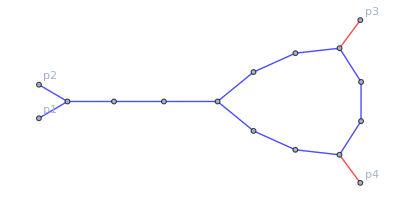
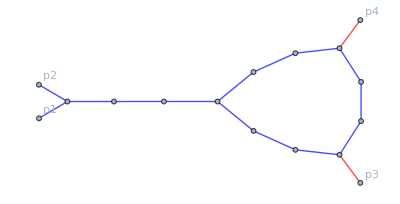
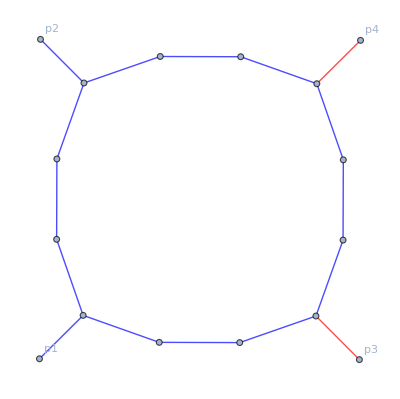
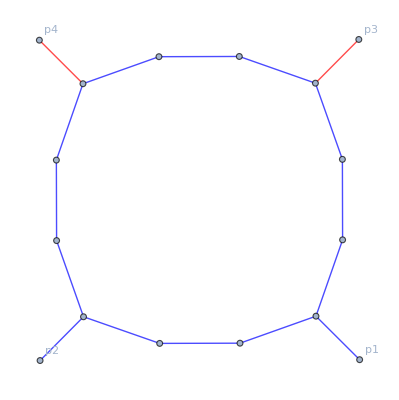
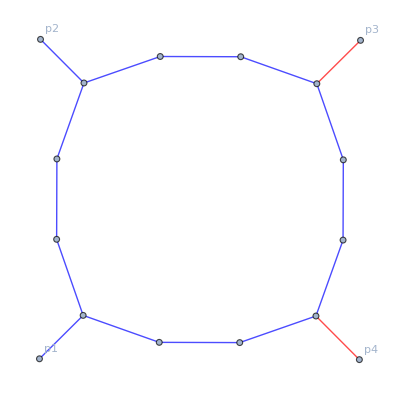
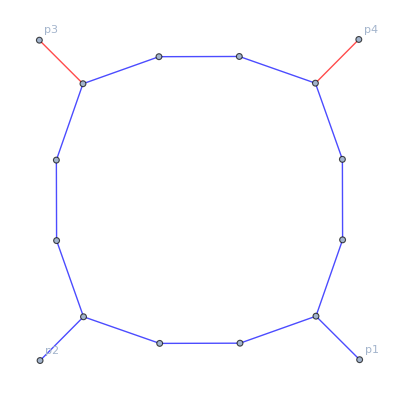
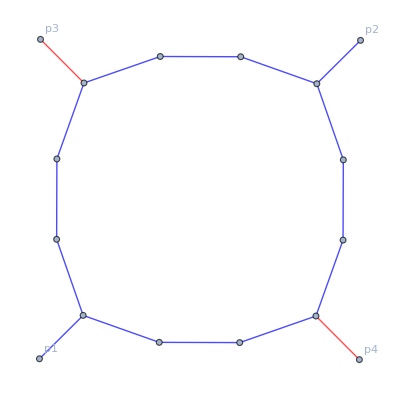
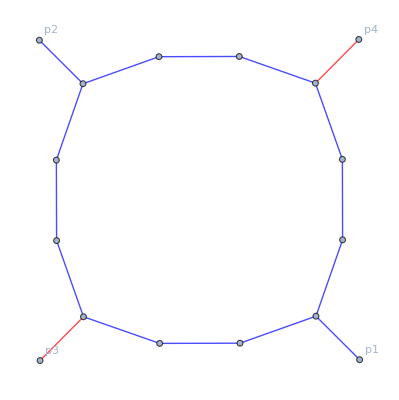

```mathematica
ToGraphRH/@ggHH
```

```mathematica
ggHH[[1]]
```

QGraph[-1,cpol[gluon[-3,p2]],cpol[gluon[-1,p1]],pol[higgs[-4,p4]],pol[higgs[-2,p3]],prop[gluon[1,-p1-p2],gluon[2,-p1-p2]],prop[t[3,-k1],tbar[4,-k1]],prop[t[5,-k1-p3],tbar[6,-k1-p3]],prop[t[7,-k1+p4],tbar[8,-k1+p4]],v3[gluon[-1,p1],gluon[-3,p2],gluon[1,-p1-p2]],v3[tbar[4,k1],higgs[-4,-p4],t[7,-k1+p4]],v3[tbar[6,k1+p3],higgs[-2,-p3],t[3,-k1]],v3[tbar[8,k1-p4],gluon[2,p1+p2],t[5,-k1-p3]]]

## Translation in graph - friendly format

```mathematica
(*TODO: generic vertices*)

next=4;
nint=4;
nvert=4;

f=(ToString/*StringDelete[Shortest["["~~___~~"]"]]);
f[ggHH[[1]][[1+1]][[1]] ]

extE=Table[{100+i,ggHH[[1]][[i+1]][[1]][[1]],f[ggHH[[1]][[i+1]][[1]]]},{i,1,next}]

intE=Table[{ggHH[[1]][[i+1]][[1]][[1]],ggHH[[1]][[i+1]][[2]][[1]],f[ggHH[[1]][[i+1]][[1]]]},{i,next+1,next+nint}]

verts3= Table[{ggHH[[1]][[i+1]][[1]][[1]]->ggHH[[1]][[i+1]][[2]][[1]],ggHH[[1]][[i+1]][[3]][[1]]->ggHH[[1]][[i+1]][[2]][[1]]},{i,next+nint+1,next+nint+nvert}]

totE=Join[extE,intE]/.Flatten[verts3]
```

gluon

{{101,-3,gluon},{102,-1,gluon},{103,-4,higgs},{104,-2,higgs}}

{{1,2,gluon},{3,4,t},{5,6,t},{7,8,t}}

{{-1→-3,1→-3},{4→-4,7→-4},{6→-2,3→-2},{8→2,5→2}}

{{101,-3,gluon},{102,-3,gluon},{103,-4,higgs},{104,-2,higgs},{-3,2,gluon},{-2,-4,t},{2,-2,t},{-4,2,t}}

## Enumerate spanning trees and Cutkosky cuts and Bubble cuts

### Spanning Trees

```mathematica
vertices[preceding_]:=DeleteDuplicates[Flatten[Table[{preceding[[i]][[1]],preceding[[i]][[2]]},{i,1,Length[preceding]}]]]

condition[edge_, preceding_]:=If[
Or[MemberQ[vertices[preceding],edge[[1]]]==True && MemberQ[vertices[preceding],edge[[2]]]==False, 
MemberQ[vertices[preceding],edge[[1]]]==False && MemberQ[vertices[preceding],edge[[2]]]==True]==True,
 True, False]

possibledges[preceding_, totE_]:=Module[{conditionin},
conditionin[edge_]:=condition[edge,preceding];
Select[totE,conditionin]
]

adjacent[v_,totE_]:=Module[{condition},
condition[e_]:=If[Or[e[[1]]==v , e[[2]]==v]==True,True,False];
Select[totE,condition]
]

adder[precedingtree_,totE_, oneorall_]:=Module[{edges,newtrees},
edges=possibledges[precedingtree,totE];
If[Length[edges]>0,
newtrees=If[oneorall==0,Table[Join[precedingtree,{edges[[i]]}],{i,1,Length[edges]}],{Join[precedingtree,{edges[[1]]}]}],
newtrees=precedingtree
];
newtrees
]

iterator[previoustrees_,totE_,oneorall_]:=Module[{nexttrees},
nexttrees=Flatten[Table[adder[previoustrees[[i]],totE,oneorall],{i,1,Length[previoustrees]}],1];
nexttrees
]
(*
spanningTreeGenerator[totE_,nvert_]:=Module[{v,initialtrees},
v=totE[[1]][[1]];
initialtrees=Table[{adjacent[v,totE][[i]]},{i,1,Length[adjacent[v,totE]]}];
For[j=0,j<nvert-2,j++, initialtrees=iterator[initialtrees,totE]];
initialtrees
]*)

spanningTreeGenerator[totE_,nvert_,initialv_,oneorall_]:=Module[{v,initialtrees},
v=initialv;
initialtrees=If[oneorall==0,Table[{adjacent[v,totE][[i]]},{i,1,Length[adjacent[v,totE]]}], {{adjacent[v,totE][[1]]}}];
If[nvert>2,
For[j=0,j<nvert-2,j++, If[ Length[possibledges[initialtrees[[1]], totE]]>0,initialtrees=iterator[initialtrees,totE,oneorall], initialtrees=initialtrees]]];
initialtrees
]

finalSpanningTree[totE_,nvert_,initialv_,oneorall_]:=DeleteDuplicates[Table[Sort[Sort[spanningTreeGenerator[totE,nvert,initialv,oneorall][[p]],#1[[2]]<#2[[2]]& ],#1[[1]]<#2[[1]]& ],{p,1,Length[spanningTreeGenerator[totE,nvert,initialv,oneorall]]}]]


sptree=finalSpanningTree[{{1,2,glu},{2,3,h},{3,4,g},{4,1,t},{3,5,z},{5,6,h},{6,4,f}},6,1,1]
```

{{{1,2,glu},{2,3,h},{3,5,z},{3,4,g},{5,6,h}}}

### Cutkosky cuts

```mathematica
(*Given a spanning tree and an edge in the spanning tree, construct the two disconnected graphs*)
(*TODO: number of jets*)
(*TODO: flavourful cuts*)

subgraphGenerator[spanningtree_,edge_,nvert_,totE_]:=Module[{twoTrees,onetree,othertree,onevertices,i,bothContained,cutkoskyCut,onceContained,leftGraph},
twoTrees=Complement[spanningtree,{edge}];
onetree=finalSpanningTree[twoTrees, nvert,totE[[1]][[1]],1][[1]];
othertree=Complement[twoTrees,onetree];
onevertices=DeleteDuplicates[Join[Table[onetree[[i]][[1]],{i,1,Length[onetree]}],Table[onetree[[i]][[2]],{i,1,Length[onetree]}]]];
onceContained[edgy_]:=If[Length[Complement[{edgy[[1]],edgy[[2]]},onevertices]]==1, True,False];
bothContained[edgy_]:=If[Length[Complement[{edgy[[1]],edgy[[2]]},onevertices]]==2, True,False];
leftGraph=Select[totE,bothContained];
cutkoskyCut=Select[totE,onceContained];
{cutkoskyCut,leftGraph}
]

sptree[[1]]
subgraphGenerator[{{1,2,glu},{2,3,h},{3,5,z},{5,6,h},{6,4,f}},{3,5,z},6,{{1,2,glu},{2,3,h},{3,4,g},{4,1,t},{3,5,z},{5,6,h},{6,4,f}}]
```

{{1,2,glu},{2,3,h},{3,5,z},{3,4,g},{5,6,h}}

{{{3,4,g},{4,1,t},{3,5,z}},{{5,6,h},{6,4,f}}}

### Bubble cuts

```mathematica
(*use boundary function and spanning tree generator at step i*)

boundary[s_,edgeSet_]:=Module[{condition},
condition[edge_]:=If[Length[Complement[{edge[[1]],edge[[2]]},s]]==1,True,False];
Select[edgeSet,condition]
]

bubbleFinder[subgraph_, cutkoskyCuts_,nvert_]:=Module[{extVert,final={}},
extVert=Intersection[Join[Table[cutkoskyCuts[[i]][[1]],{i,1,Length[cutkoskyCuts]}],Table[cutkoskyCuts[[i]][[2]],{i,1,Length[cutkoskyCuts]}]],Join[Table[subgraph[[i]][[1]],{i,1,Length[subgraph]}],Table[subgraph[[i]][[2]],{i,1,Length[subgraph]}]]];
Print[extVert];
For[l=1,l≤Length[extVert],l++, (*Print[boundary[Join[Table[finalSpanningTree[subgraph,1+2,extVert[[l]],1][[1]][[j]][[1]],{j,1,Length[finalSpanningTree[subgraph,k+2,extVert[[l]],1][[1]]]}],
Table[finalSpanningTree[subgraph,1+2,extVert[[l]],1][[1]][[j]][[2]],{j,1,Length[finalSpanningTree[subgraph,k+2,extVert[[l]],1][[1]]]}]],subgraph]]*)
For[k=1,k≤nvert-2,k++,
If[ 
Length[boundary[Join[Table[finalSpanningTree[subgraph,k+1,extVert[[l]],1][[1]][[j]][[1]],{j,1,Length[finalSpanningTree[subgraph,k+1,extVert[[l]],1][[1]]]}],
Table[finalSpanningTree[subgraph,k+1,extVert[[l]],1][[1]][[j]][[2]],{j,1,Length[finalSpanningTree[subgraph,k+1,extVert[[l]],1][[1]]]}]],subgraph]]==1,
final=Join[final,Join[Table[finalSpanningTree[subgraph,k+1,extVert[[l]],1][[1]][[j]][[1]],{j,1,Length[finalSpanningTree[subgraph,k+1,extVert[[l]],1][[1]]]}],
Table[finalSpanningTree[subgraph,k+1,extVert[[l]],1][[1]][[j]][[2]],{j,1,Length[finalSpanningTree[subgraph,k+1,extVert[[l]],1][[1]]]}]]]
]
]
];
final
]

bubbleFinder[{{1,2},{2,102},{2,3},{3,4},{3,4}},{{4,104},{1,101}},4]

Length[boundary[finalSpanningTree[{{1,2},{2,102},{2,3},{3,4},{3,4}},2,4,1][[1]][[1]],{{1,2},{2,102},{2,3},{3,4},{3,4}}]]

Length[boundary[Join[Table[finalSpanningTree[{{1,2},{2,102},{2,3},{3,4},{3,4}},2,4,1][[1]][[j]][[1]],{j,1,Length[finalSpanningTree[{{1,2},{2,102},{2,3},{3,4},{3,4}},2,4,1][[1]]]}],
Table[finalSpanningTree[{{1,2},{2,102},{2,3},{3,4},{3,4}},2,4,1][[1]][[j]][[2]],{j,1,Length[finalSpanningTree[{{1,2},{2,102},{2,3},{3,4},{3,4}},2,4,1][[1]]]}]],{{1,2},{2,102},{2,3},{3,4},{3,4}}]]==1
```

{1,4}

{3,4}

1

True